## Listening to result Temp : 0.75

```mathematica
file=First@FileNames["output*.txt", NotebookDirectory[]]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/prep/Chopin only/output.txt

```mathematica
composition=Import[file];
```

```mathematica
letters=Take[Flatten[Transpose@{ToUpperCase@Alphabet[], StringJoin@@@Transpose@{Evaluate@ToUpperCase@Alphabet[], Table["#", {Length@Alphabet[]}]}}, 1], 14]
```

{A,A#,B,B#,C,C#,D,D#,E,E#,F,F#,G,G#}

```mathematica
inverseConversionTable=Rule@@@Evaluate@(Transpose@{Table[i, {i, 0, Length@letters-1}],letters})
```

{0→A,1→A#,2→B,3→B#,4→C,5→C#,6→D,7→D#,8→E,9→E#,10→F,11→F#,12→G,13→G#}

```mathematica
rows=(Thread@ToExpression@#&/@(StringSplit[#, "\t"]&/@StringSplit[composition, "\n"]));
```

```mathematica
Take[rows, 10]
```

{{5,10,6,6},{19,25,10,5,25,10,5,25,10,5},{3,10,13,2},{10,20,10,4,20,1,3,20,10,3},{3,55,4,5},{14,20,10,3},{20,20,10,4,20,1,3},{20,20,4,3},{19,20,1,2},{3,10,4,5}}

```mathematica
notes=Partition[Drop[#, 1], 3]&/@rows;
```

```mathematica
times=rows⟦All,1⟧;
```

```mathematica
toNote[numbers_]:=Flatten[{#⟦1⟧,((#⟦2⟧/.inverseConversionTable)<>ToString@#⟦3⟧)}&/@numbers, 1]
```

```mathematica
theNotesAndDurations=(Thread@toNote@#)&/@notes;
```

```mathematica
Take[theNotesAndDurations, 10]
```

{{10,D6},{25,F5,25,F5,25,F5},{10,G#2},{20,F4,20,A#3,20,F3},{55,C5},{20,F3},{20,F4,20,A#3},{20,C3},{20,A#2},{10,C5}}

```mathematica
Take[Partition[#, 2]&/@theNotesAndDurations, 10]
```

{{{10,D6}},{{25,F5},{25,F5},{25,F5}},{{10,G#2}},{{20,F4},{20,A#3},{20,F3}},{{55,C5}},{{20,F3}},{{20,F4},{20,A#3}},{{20,C3}},{{20,A#2}},{{10,C5}}}

This looks really ugly, but it converts back to {interval since last note, duration, note}

```mathematica
startTimes=FoldList[#1+#2&,First@times, Drop[times,1 ]];
```

```mathematica
preFinal=Partition[Flatten@(Transpose@{Table[#⟦1⟧, {Length@#⟦2⟧}],#⟦2⟧}&/@(Transpose@{startTimes,Partition[#, 2]&/@theNotesAndDurations})), 3];
```

```mathematica
Take[preFinal, 10]
```

{{5,10,D6},{24,25,F5},{24,25,F5},{24,25,F5},{27,10,G#2},{37,20,F4},{37,20,A#3},{37,20,F3},{40,55,C5},{54,20,F3}}

```mathematica
final = preFinal/.{x_, y_, z_}-> {x/50, (x+y)/50, z};
```

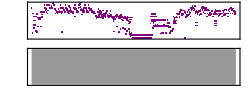

```mathematica
midi=Sound[SoundNote[Last@#, {#⟦1⟧,#⟦2⟧},"Piano", Rule["SoundVolume",0.5]]&/@final]
```

```mathematica
Export[ToFileName[{NotebookDirectory[]}, "output.mid"], midi]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/prep/Chopin only/output.mid

## Listening to result Temp : 0.7

```mathematica
file=First@FileNames["output*.txt", NotebookDirectory[]]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/prep/Chopin only/output.txt

```mathematica
composition=Import[file];
```

```mathematica
letters=Take[Flatten[Transpose@{ToUpperCase@Alphabet[], StringJoin@@@Transpose@{Evaluate@ToUpperCase@Alphabet[], Table["#", {Length@Alphabet[]}]}}, 1], 14]
```

{A,A#,B,B#,C,C#,D,D#,E,E#,F,F#,G,G#}

```mathematica
inverseConversionTable=Rule@@@Evaluate@(Transpose@{Table[i, {i, 0, Length@letters-1}],letters})
```

{0→A,1→A#,2→B,3→B#,4→C,5→C#,6→D,7→D#,8→E,9→E#,10→F,11→F#,12→G,13→G#}

```mathematica
rows=(Thread@ToExpression@#&/@(StringSplit[#, "\t"]&/@StringSplit[composition, "\n"]));
```

```mathematica
Take[rows, 10]
```

{{5,10,6,6},{19,25,10,5,25,10,5,25,10,5},{3,10,13,2},{10,20,10,4,20,1,3,20,10,3},{3,55,4,5},{14,20,10,3},{20,20,10,4,20,1,3},{20,20,4,3},{19,20,1,2},{3,10,4,5}}

```mathematica
notes=Partition[Drop[#, 1], 3]&/@rows;
```

```mathematica
times=rows⟦All,1⟧;
```

```mathematica
toNote[numbers_]:=Flatten[{#⟦1⟧,((#⟦2⟧/.inverseConversionTable)<>ToString@#⟦3⟧)}&/@numbers, 1]
```

```mathematica
theNotesAndDurations=(Thread@toNote@#)&/@notes;
```

```mathematica
Take[theNotesAndDurations, 10]
```

{{10,D6},{25,F5,25,F5,25,F5},{10,G#2},{20,F4,20,A#3,20,F3},{55,C5},{20,F3},{20,F4,20,A#3},{20,C3},{20,A#2},{10,C5}}

```mathematica
Take[Partition[#, 2]&/@theNotesAndDurations, 10]
```

{{{10,D6}},{{25,F5},{25,F5},{25,F5}},{{10,G#2}},{{20,F4},{20,A#3},{20,F3}},{{55,C5}},{{20,F3}},{{20,F4},{20,A#3}},{{20,C3}},{{20,A#2}},{{10,C5}}}

This looks really ugly, but it converts back to {interval since last note, duration, note}

```mathematica
startTimes=FoldList[#1+#2&,First@times, Drop[times,1 ]];
```

```mathematica
preFinal=Partition[Flatten@(Transpose@{Table[#⟦1⟧, {Length@#⟦2⟧}],#⟦2⟧}&/@(Transpose@{startTimes,Partition[#, 2]&/@theNotesAndDurations})), 3];
```

```mathematica
Take[preFinal, 10]
```

{{5,10,D6},{24,25,F5},{24,25,F5},{24,25,F5},{27,10,G#2},{37,20,F4},{37,20,A#3},{37,20,F3},{40,55,C5},{54,20,F3}}

```mathematica
final = preFinal/.{x_, y_, z_}-> {x/50, (x+y)/50, z};
```

```mathematica
midi=Sound[SoundNote[Last@#, {#⟦1⟧,#⟦2⟧},"Piano", Rule["SoundVolume",0.5]]&/@final]
```

-Graphics-

```mathematica
Export[ToFileName[{NotebookDirectory[]}, "output.mid"], midi]
```

/Users/seantokunaga/Documents/Repositories/char-rnn/prep/Chopin only/output.mid